```mathematica
Subscript[x, 1][t_] := 2*Cos[t]+Cos[2*t]
```

```mathematica
Subscript[x, 1]'[t]
```

-2 Sin[t]-2 Sin[2 t]

```mathematica
Subscript[x, 1]''[t]
```

-2 Cos[t]-4 Cos[2 t]

```mathematica
Subscript[x, 2][t_]=2*Sin[t]-Sin[2*t]
```

2 Sin[t]-Sin[2 t]

```mathematica
Subscript[x, 2]'[t]
```

2 Cos[t]-2 Cos[2 t]

```mathematica
Subscript[x, 2]''[t]
```

-2 Sin[t]+4 Sin[2 t]

```mathematica
FullSimplify[(Subscript[x, 1]'[t]*Subscript[x, 2]''[t]-Subscript[x, 1]''[t]*Subscript[x, 2]'[t])/(((Subscript[x, 1]'[t])^2+(Subscript[x, 2]'[t])^2)^(3/2))]
```

-1/(4 √(2-2 Cos[3 t]))

```mathematica
Abs[-3]
```

3

```mathematica
FullSimplify[Abs[(((Subscript[x, 1]'[t])^2+(Subscript[x, 2]'[t])^2)^(3/2))/(Subscript[x, 1]'[t]*Subscript[x, 2]''[t]-Subscript[x, 1]''[t]*Subscript[x, 2]'[t])]]
```

4 √2 √Abs[1-Cos[3 t]]

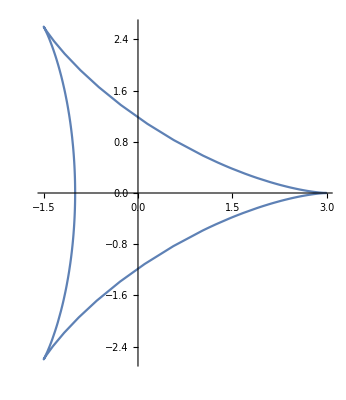

```mathematica
ParametricPlot[{Subscript[x, 1][t], Subscript[x, 2][t]}, {t,0,2*π}]
```

```mathematica
D[{Subscript[x, 1][t], Subscript[x, 2][t]},t]
```

{-2 Sin[t]-2 Sin[2 t],2 Cos[t]-2 Cos[2 t]}

```mathematica
Norm[{Subscript[x, 1][t], Subscript[x, 2][t]}]
```

√(Abs[2 Cos[t]+Cos[2 t]]^2+Abs[2 Sin[t]-Sin[2 t]]^2)

```mathematica
Simplify[{Subscript[x, 1][t], Subscript[x, 2][t]}+1/((-1/(4 √(2-2 Cos[3 t])))*Norm[D[{Subscript[x, 1][t], Subscript[x, 2][t]},t]])*{-Subscript[x, 2]'[t],Subscript[x, 1]'[t]}]
```

{2 Cos[t]+Cos[2 t]+8 (Cos[t]-Cos[2 t]) √(Sin[(3 t)/2]^2/(Abs[Cos[t]-Cos[2 t]]^2+Abs[Sin[t]+Sin[2 t]]^2)),2 Sin[t]-Sin[2 t]+8 √(Sin[(3 t)/2]^2/(Abs[Cos[t]-Cos[2 t]]^2+Abs[Sin[t]+Sin[2 t]]^2)) (Sin[t]+Sin[2 t])}

```mathematica
FullSimplify[Subscript[x, 1][t]+(1/((-1/(4 √(2-2 Cos[3 t])))*Norm[D[{Subscript[x, 1][t], Subscript[x, 2][t]},t]]))*(-Subscript[x, 2]'[t])]
```

2 Cos[t]+Cos[2 t]+8 (Cos[t]-Cos[2 t]) √(Sin[(3 t)/2]^2/(Abs[Cos[t]-Cos[2 t]]^2+Abs[Sin[t]+Sin[2 t]]^2))

```mathematica
FullSimplify[Subscript[x, 2][t]+(1/((-1/(4 √(2-2 Cos[3 t])))*Norm[D[{Subscript[x, 1][t], Subscript[x, 2][t]},t]]))*(Subscript[x, 1]'[t])]
```

2 Sin[t]-Sin[2 t]+8 √(Sin[(3 t)/2]^2/(Abs[Cos[t]-Cos[2 t]]^2+Abs[Sin[t]+Sin[2 t]]^2)) (Sin[t]+Sin[2 t])